```mathematica
#stabilizers;
S1 = {1, 1, 0};
S2 = {0, 1, 1};
#list#of#values#of#p;
x = {};
#list#of#sucsessful#events#over#total#events;
lstPcorr = {};
#number #of#events;
R=100;
#loop#over#range #of #p;
Do[
#lists #each #time#correctable #state #enountered;
sucess = {};

Do[
#generates#1 #or #0 #randomly;
X1 =RandomVariate[BinomialDistribution[1, i]];
X2=RandomVariate[BinomialDistribution[1, i]];
X3=RandomVariate[BinomialDistribution[1, i]];
stab = {S1, S2};
error = {X1, X2, X3};
 #multiplying #the #stabilizers #by #the #error;
S1err= stab[[1]]*error;
S2err = stab[[2]]*error;
#checks#parity #to #give #syndrome;
syndrome1 = Mod[Total[S1err], 2];
syndrome2 = Mod[Total[S2err], 2];
syndrome = {syndrome1, syndrome2};
#assosiartes #syndrome #with #an #error;
as = <|{0, 0} ->  {0, 0, 0}, {1, 0} -> {1, 0, 0},  {1, 1} ->  {0, 1, 0}, {0, 1} -> {0, 0, 1} |>;
#adds#correction#to #the #syndrome;
EplusC = error + as[syndrome];
#logical#error#for#3#qubit;
zlogical = {1, 1, 1};
#checks #commutation #of #error #with #logical #state; 
a = Position[EplusC, 1];
b = Position[zlogical, 1];
#appends #to #sucess #if #errors #do #not #commute ;
If[a ≠ b, AppendTo[sucess, 1], AppendTo[sucess, 0] ]
, {R}];
#gives#the#correction#probability;
Pcorr = Total[sucess]/R ;
AppendTo[lstPcorr, Pcorr];
AppendTo[x, i];

,{i, 0, 1,0.1}]


#puts#results #into #correct #format #for #listplot #function;
```

```mathematica
z= {};
Do[ y = {x[[n]] ,lstPcorr[[n]]};
AppendTo[z, y];
,{n,1, 11, 1}]
Print[z]
```

{{0.,1},{0.1,97/100},{0.2,9/10},{0.3,71/100},{0.4,3/5},{0.5,21/50},{0.6,8/25},{0.7,7/25},{0.8,9/100},{0.9,1/50},{1.,0}}

```mathematica
#plot #of #the #results;
```

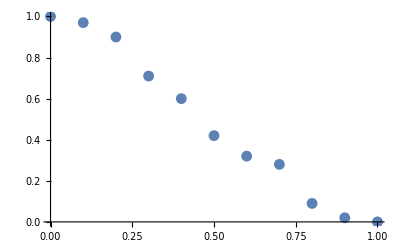

```mathematica
ListPlot[z,PlotRange->{{0,1},{0,1}}]
```